Sampling

### Logistic Function

```mathematica
Logistic[x_]:= 1/(1+Exp[-x])
```

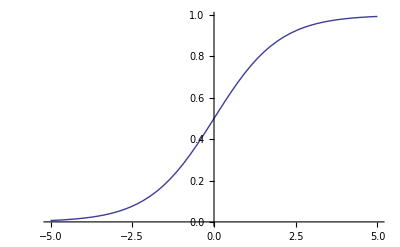

```mathematica
Plot[Logistic[x],{x,-5,5}]
```

### Main Functions

```mathematica
Weight[m_,n_]:=RandomReal[{-1,1},{m,n}]
Visibles[m_]:=RandomInteger[1,m]
Hiddens[n_]:=RandomInteger[1,n]
BiasHiddenSampling[n_]:=RandomInteger[0,n]
BiasVisibleSampling[m_]:=RandomInteger[0,m]
```

### Declarations

```mathematica
SeedRandom[1]
W=Weight[4,5]
V=Visibles[4]
H=Hiddens[5]
BH=BiasHiddenSampling[5]
BV=BiasVisibleSampling[4]
```

{{0.634779,-0.777161,0.579052,-0.624394,-0.517278},{-0.868522,0.0844932,-0.537691,-0.207988,0.400948},{-0.576348,0.497314,-0.154299,-0.50501,0.954344},{0.650326,0.85055,0.156112,-0.414261,-0.583898}}

{1,0,0,1}

{0,1,0,0,1}

{0,0,0,0,0}

{0,0,0,0}

```mathematica
dataV=Table[Visibles[4],{i,10}]
```

{{1,0,0,1},{0,1,0,1},{0,1,0,0},{1,0,1,1},{1,1,1,0},{1,0,1,0},{0,1,1,1},{0,1,0,1},{0,1,0,0},{0,0,0,1}}

```mathematica
V2=Visibles[4]
```

{1,0,1,0}

```mathematica
V3=Visibles[4]
```

{0,0,0,0}

### Sampling Functions

```mathematica
sample[l_]:=Map[RandomVariate[BernoulliDistribution[#]]&,l]
```

```mathematica
SampleHidden[w_,bh_][v_]:=sample[Logistic@(wᵀ.v+bh)]
SampleVisible[w_,bv_][h_]:=sample[Logistic@(w.h+bv)]
HiddenProbabilities[w_,bh_][v_]:=Logistic@(wᵀ.v+bh);
VisibleProbabilities[w_,bv_][h_]:=Logistic@(w.h+bv);
```

```mathematica
Mean[Table[N @ SampleHidden[W,0*BH ][V],{1000}]]
SampleVisible[W,BV][H]
```

{0.336,0.59,0.522,0.492,0.839}

{1,1,1,1}

```mathematica
W1=Weight[4,5]
```

{{-0.571793,-0.288723,0.928686,0.308795,0.468072},{0.450696,-0.605276,0.300727,-0.767229,-0.98279},{-0.484121,-0.189034,-0.200429,-0.362719,0.168117},{-0.759685,0.307014,-0.0368698,-0.864111,0.297861}}

```mathematica
W2=Weight[4,5]
```

{{0.0526673,0.202912,0.933782,-0.232647,0.0119456},{-0.751207,-0.82033,0.314438,0.298074,-0.197246},{0.22064,-0.616921,-0.429878,-0.31569,0.879237},{-0.334777,0.46148,0.591179,-0.123618,-0.495661}}

```mathematica
W3=W3+0.1*(W1+W2)
```

{{-0.103825,-0.017162,0.372494,0.0152296,0.0960034},{-0.0601023,-0.285121,0.123033,-0.0938311,-0.236007},{-0.0526963,-0.161191,-0.126061,-0.135682,0.209471},{-0.218892,0.153699,0.110862,-0.197546,-0.0395599}}

```mathematica
BitXor[{1,0,1},{1,0,0,1}]
```

Thread::tdlen: Objects of unequal length in BitXor[{1, 0, 1}, {1, 0, 0, 1}] cannot be combined.

```mathematica
Outer[BitXor8,{1,0,1,0},{1,0,0,1}]
```

{{BitXor8[1,1],BitXor8[1,0],BitXor8[1,0],BitXor8[1,1]},{BitXor8[0,1],BitXor8[0,0],BitXor8[0,0],BitXor8[0,1]},{BitXor8[1,1],BitXor8[1,0],BitXor8[1,0],BitXor8[1,1]},{BitXor8[0,1],BitXor8[0,0],BitXor8[0,0],BitXor8[0,1]}}

## Learning

```mathematica
ClearAll[DataLearning,DeltaWeight]
```

```mathematica
DeltaWeight[bh_,bv_,ϵ_,v1_][w_]:=Module[{h1,v2,h2,w0,w1,wnew},
wnew=w;
Do[
h1=SampleHidden[w,bh][v1];
v2=SampleVisible[w,bv][h1];
h2=SampleHidden[w,bh][v2];
w0=1-Outer[BitXor,v1,h1];
w1=1-Outer[BitXor,v1,h2];
wnew+= ϵ*(w0-w1);
,
{4}];
wnew
]
```

```mathematica
DataLearning[w_,bh_,bv_,ϵ_,n_,dataV_]:=Nest[Function[DeltaWeight[bh,bv,ϵ,RandomChoice[dataV]][#]],w,n]
```

## Testing

```mathematica
SeedRandom[4];
BH1=RandomInteger[0,2];
BV1=RandomInteger[0,4];
W=RandomReal[{-0.1,0.1},{4,2}]
dataV={{0,0,0,0},{0,0,0,0},{0,0,0,0},{1,1,1,1},{1,1,1,1},{1,1,1,1}};
w1=DataLearning[W,BH1,BV1,0.01,5000,dataV]
l1=
VisibleProbabilities[w1,BV1] /@ {{0,0},{0,1},{1,0},{1,1}};
ArrayPlot[l1,PixelConstrained->10]
l1
```

{{-0.0377248,0.0132008},{0.0254311,-0.0741373},{0.0583272,0.0308817},{-0.0786434,-0.0276381}}

{{-34.8677,33.5332},{-34.8046,33.4459},{-34.7717,33.5509},{-34.9086,33.4924}}

-Graphics-

{{0.5,0.5,0.5,0.5},{1.,1.,1.,1.},{7.1968×10^-16,7.66598×10^-16,7.92236×10^-16,6.90826×10^-16},{0.208412,0.204451,0.227797,0.195245}}